# Yoosook' s Request

## Functions

```mathematica
ReadDataset[path_,thresholds_]:=Module[{raw,clean,expTuples},
raw=Import[path];
clean=#[[1;;(1+Length[thresholds])]]&/@raw;
expTuples={GetExperimentID[#[[1]]],#[[2;;All]]}&/@clean;
expTuples//Sort
]
GetExperimentID[expStr_]:=ToExpression[#]&/@StringSplit[expStr,"_"][[2;;All]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
ColorBlend[a_]:=Blend[{{0,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.35,Directive[RGBColor[0, 0.8, 1],Opacity[1]]},{.65,Directive[RGBColor[1, 0.8, 1],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},a]
```

## Load Data

```mathematica
SetDirectory["/Volumes/marshallShare/UCI/Yoosook/yParams/island/"];
{thresholds,POPSIZE}={{.25,.50,.75,.90,.95},1000000};
(*Load Data*)
expTuples=ReadDataset["./thresholdCrosses.csv",thresholds];
paramsRanges=DeleteDuplicates[#]&/@(expTuples[[All,1]]//Transpose)
(* Key: {releaseRatio, releasePattern, fitnessCost, standingVariation}*)
```

{{100,133,200,400,571,1000,1333,2000,4000,10000,20000,40000,100000,250000,500000,1000000},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53},{100},{1,5,10,50,100,500,1000}}

## Export Response Curves

```mathematica
Table[
Table[
trends=Table[
{thresholdIx,releases,standingVar}={j,rel,svar};
filtered=Cases[expTuples,{{_,releases,_,standingVar},_}];
tuples={#[[1,1]]/1000000,#[[2,thresholdIx]]/365}&/@filtered
,{rel,paramsRanges[[2]]}];
linePlot=ListLogLogPlot[trends
,AspectRatio->1
,Epilog->Flatten[{PointSize[Medium],Opacity[1],(Point[#]&/@tuples)}]
,Frame->True
(*,FrameLabel->(Style[#,30]&/@{
"Release Fraction", 
"Years to "<>ToString[thresholds[[thresholdIx]]]
})*)
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicks->None
,FrameTicksStyle->Directive[20]
,GridLines->{Range[0,1,.1],{.1,.2,.5,1,2,5}}
,ImageSize->800
,InterpolationOrder->2
,Joined->True
(*,PlotLabel->Style["Standing Variation: "<>ToString[(standingVar/100000)//N],30]*)
,PlotMarkers->{None, 10}
,PlotRange->{{10^-4,1},{0.05,5}}
,PlotStyle->({Thickness[.006],ColorBlend[#]}&/@Range[0,1,1/Length[paramsRanges[[2]]]])
];
Export[
"./img/CR"<>"_"<>
StringPadLeft[ToString[Round[thresholds[[thresholdIx]]*1000]],4,"0"]<>
"_"<>StringPadLeft[ToString[standingVar],4,"0"]<>".pdf"
,linePlot
,ImageResolution-> 750
]
,{svar,paramsRanges[[-1]]}]
,{j,1,5}]
```

{{./img/CR_0250_0001.pdf,./img/CR_0250_0005.pdf,./img/CR_0250_0010.pdf,./img/CR_0250_0050.pdf,./img/CR_0250_0100.pdf,./img/CR_0250_0500.pdf,./img/CR_0250_1000.pdf},{./img/CR_0500_0001.pdf,./img/CR_0500_0005.pdf,./img/CR_0500_0010.pdf,./img/CR_0500_0050.pdf,./img/CR_0500_0100.pdf,./img/CR_0500_0500.pdf,./img/CR_0500_1000.pdf},{./img/CR_0750_0001.pdf,./img/CR_0750_0005.pdf,./img/CR_0750_0010.pdf,./img/CR_0750_0050.pdf,./img/CR_0750_0100.pdf,./img/CR_0750_0500.pdf,./img/CR_0750_1000.pdf},{./img/CR_0900_0001.pdf,./img/CR_0900_0005.pdf,./img/CR_0900_0010.pdf,./img/CR_0900_0050.pdf,./img/CR_0900_0100.pdf,./img/CR_0900_0500.pdf,./img/CR_0900_1000.pdf},{./img/CR_0950_0001.pdf,./img/CR_0950_0005.pdf,./img/CR_0950_0010.pdf,./img/CR_0950_0050.pdf,./img/CR_0950_0100.pdf,./img/CR_0950_0500.pdf,./img/CR_0950_1000.pdf}}

```mathematica
Table[
trends=Table[
{thresholdIx,releases,standingVar}={2,rel,svar};
filtered=Cases[expTuples,{{_,releases,_,standingVar},_}];
tuples={#[[1,1]]/1000000,#[[2,thresholdIx]]/365}&/@filtered
,{rel,paramsRanges[[2]]}];
linePlot=ListLogLogPlot[trends
,AspectRatio->1
,Epilog->Flatten[{PointSize[Medium],Opacity[1],(Point[#]&/@tuples)}]
,Frame->True
(*,FrameLabel->(Style[#,30]&/@{
"Release Fraction", 
"Years to "<>ToString[thresholds[[thresholdIx]]]
})*)
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicks->{Range[0,1,.3], Range[0,5]}
,FrameTicksStyle->Directive[20]
,GridLines->{Range[0,1,.1],{.1,.2,.5,1,2,5}}
,ImageSize->800
,InterpolationOrder->1
,Joined->True
(*,PlotLabel->Style["Standing Variation: "<>ToString[(standingVar/100000)//N],30]*)
,PlotMarkers->{None, 10}
,PlotRange->{{10^-4,1},{0.05,5}}
,PlotStyle->({Thickness[.006],ColorBlend[#]}&/@Range[0,1,1/Length[paramsRanges[[2]]]])
]
,{svar,paramsRanges[[-1]]}];
```

## Export Response Surfaces

```mathematica
Table[
{thresholdIx,standingVar}={i,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuples={Log[N[#[[1,1]]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
Cases[tuples,{a_,b_,c_}/;c≤13]//Sort;
(**)
yLabels=DeleteDuplicates[{Log[N[#[[1,2]]]],N[#[[1,2]]]}&/@filtered][[2;; ;;4]];
xLabels=DeleteDuplicates[{Log[N[#[[1,1]]]/1000000],NumberForm[N[#[[1,1]]]/1000000,{1,4}]}&/@filtered][[2;; ;;4]];
cf=ListContourPlot[tuples
,ClippingStyle->{RGBColor[1, 0, 0],White}
,Contours->10
,ContourStyle->Directive[{Black, Opacity[1]}]
,ColorFunction->(ColorBlend[#]&)
,ColorFunctionScaling->True
,Epilog->Flatten[{PointSize[.0025],Opacity[.5],(Point[#[[1;;2]]]&/@tuples)}]
(*,FrameLabel->(Style[#,50]&/@{"Release Ratio","Weekly Releases"})*)
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->None
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->750
,InterpolationOrder->1
,Mesh->All
,MeshStyle->Directive[ White, Opacity[.25]]
(*,PlotLabel->Style["Weeks to: "<>ToString[thresholds[[thresholdIx]]],50,Black]*)
,PlotLegends->None
,PlotRange->{All,All,{8,52}}(*{0, 260}}*)
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
];
Export["./img/RS_"<>StringPadRight[ToString[thresholds[[thresholdIx]]*100],2,"0"]<>".pdf",cf]
,{i,1,5}]
```

{./img/RS_25.pdf,./img/RS_50.pdf,./img/RS_75.pdf,./img/RS_90.pdf,./img/RS_95.pdf}

```mathematica
{thresholdIx,standingVar}={5,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuples={N[#[[1,1]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
Cases[tuples,{a_,b_,c_}/;c≤4*6]//Sort
tuples[[All,3]]//Min
```

{{0.25,13,24.},{0.25,14,23.5714},{0.25,15,23.2857},{0.25,16,23.1429},{0.25,17,23.},{0.25,18,22.8571},{0.25,19,22.8571},{0.25,20,22.7143},{0.25,21,22.7143},{0.25,22,22.7143},{0.25,23,22.7143},{0.25,24,22.7143},{0.25,25,22.7143},{0.25,26,22.7143},{0.25,27,22.7143},{0.25,28,22.7143},{0.25,29,22.7143},{0.25,30,22.7143},{0.25,31,22.7143},{0.25,32,22.7143},{0.25,33,22.7143},{0.25,34,22.7143},{0.25,35,22.7143},{0.25,36,22.7143},{0.25,37,22.7143},{0.25,38,22.7143},{0.25,39,22.7143},{0.25,40,22.7143},{0.25,41,22.7143},{0.25,42,22.7143},{0.25,43,22.7143},{0.25,44,22.7143},{0.25,45,22.7143},{0.25,46,22.7143},{0.25,47,22.7143},{0.25,48,22.7143},{0.25,49,22.7143},{0.25,50,22.7143},{0.25,51,22.7143},{0.25,52,22.7143},{0.25,53,22.7143},{0.5,7,23.1429},{0.5,8,22.},{0.5,9,21.2857},{0.5,10,20.7143},{0.5,11,20.4286},{0.5,12,20.2857},{0.5,13,20.1429},{0.5,14,20.},{0.5,15,20.},{0.5,16,20.},{0.5,17,20.},{0.5,18,20.},{0.5,19,20.},{0.5,20,20.},{0.5,21,20.},{0.5,22,20.},{0.5,23,20.},{0.5,24,20.},{0.5,25,20.},{0.5,26,20.},{0.5,27,20.},{0.5,28,20.},{0.5,29,20.},{0.5,30,20.},{0.5,31,20.},{0.5,32,20.},{0.5,33,20.},{0.5,34,20.},{0.5,35,20.},{0.5,36,20.},{0.5,37,20.},{0.5,38,20.},{0.5,39,20.},{0.5,40,20.},{0.5,41,20.},{0.5,42,20.},{0.5,43,20.},{0.5,44,20.},{0.5,45,20.},{0.5,46,20.},{0.5,47,20.},{0.5,48,20.},{0.5,49,20.},{0.5,50,20.},{0.5,51,20.},{0.5,52,20.},{0.5,53,20.},{1.,4,22.8571},{1.,5,20.8571},{1.,6,19.8571},{1.,7,19.2857},{1.,8,18.8571},{1.,9,18.7143},{1.,10,18.5714},{1.,11,18.4286},{1.,12,18.4286},{1.,13,18.4286},{1.,14,18.4286},{1.,15,18.2857},{1.,16,18.2857},{1.,17,18.2857},{1.,18,18.2857},{1.,19,18.2857},{1.,20,18.2857},{1.,21,18.2857},{1.,22,18.2857},{1.,23,18.2857},{1.,24,18.2857},{1.,25,18.2857},{1.,26,18.2857},{1.,27,18.2857},{1.,28,18.2857},{1.,29,18.2857},{1.,30,18.2857},{1.,31,18.2857},{1.,32,18.2857},{1.,33,18.2857},{1.,34,18.2857},{1.,35,18.2857},{1.,36,18.2857},{1.,37,18.2857},{1.,38,18.2857},{1.,39,18.2857},{1.,40,18.2857},{1.,41,18.2857},{1.,42,18.2857},{1.,43,18.2857},{1.,44,18.2857},{1.,45,18.2857},{1.,46,18.2857},{1.,47,18.2857},{1.,48,18.2857},{1.,49,18.2857},{1.,50,18.2857},{1.,51,18.2857},{1.,52,18.2857},{1.,53,18.2857}}

18.2857

## New Response Surfaces

```mathematica
Table[
weeksRanges={{8,12},{12, 24},{24, 52},{52,1.5*52}};
(*colorsSolid=hexToRGB[#]&/@{"#0500c7","#0a4afc","#268cff","#75c1ff", "#c6ebff"};*)
(*colorsSolid={RGBColor[1, 0, 0],RGBColor[1, 0.56, 1],RGBColor[0, 0.8, 1],RGBColor[0.0006103608758678569, 0., 0.9347219043259327]};*)
colorsSolid={RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0]};
ColorBlendA[a_]:=Blend[{{1,Directive[colorsSolid[[1]],Opacity[0]]},{0,Directive[colorsSolid[[1]],Opacity[0]]}},a];
ColorBlendB[a_]:=Blend[{{1,Directive[colorsSolid[[2]],Opacity[0]]},{0,Directive[colorsSolid[[2]],Opacity[0]]}},a];
ColorBlendC[a_]:=Blend[{{1,Directive[colorsSolid[[3]],Opacity[0]]},{0,Directive[colorsSolid[[3]],Opacity[0]]}},a];
ColorBlendD[a_]:=Blend[{{1,Directive[colorsSolid[[4]],Opacity[0]]},{0,Directive[colorsSolid[[4]],Opacity[0]]}},a];
ColorBlendX[a_]:=Blend[{{1,Directive[colorsSolid[[4]],Opacity[0]]},{0,Directive[colorsSolid[[4]],Opacity[0]]}},a];
colors={ColorBlendA,ColorBlendB,ColorBlendC,ColorBlendD};
(**)
{thresholdIx,standingVar}={i,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuples={Log[N[#[[1,1]]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
(**)
yLabels=DeleteDuplicates[{Log[N[#[[1,2]]]],N[#[[1,2]]]}&/@filtered][[2;; ;;4]];
xLabels=DeleteDuplicates[{Log[N[#[[1,1]]]/1000000],NumberForm[N[#[[1,1]]]/1000000,{1,4}]}&/@filtered][[2;; ;;4]];
cf=Table[
ListDensityPlot[tuples
,BoundaryStyle->Directive[{Black, Thickness[.005]}]
,ClippingStyle->{RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0],RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0]}
,ColorFunction->(colors[[i]][#]&)
,ColorFunctionScaling->True
,Epilog->Flatten[{PointSize[Medium],Opacity[.2],(Point[#[[1;;2]]]&/@tuples)}]
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->None
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->750
,InterpolationOrder->2
,Mesh->False
,MeshStyle->Directive[White, Opacity[.25]]
,PlotLegends->None
,PlotRange->{All,All,weeksRanges[[i]]}(*{0, 260}}*)
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
]
,{i,1,Length[weeksRanges]}];
dummy=ListDensityPlot[tuples
,BoundaryStyle->Directive[{Thin, Opacity[.025]}]
,ColorFunction->(ColorBlendX[#]&)
,Epilog->Flatten[{PointSize[Large],Opacity[.5],(Point[#[[1;;2]]]&/@tuples)}]
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,ImageSize->750
,InterpolationOrder->0
];
ca=ListContourPlot[tuples
,ClippingStyle->{White,White}
,Contours->50
,ContourStyle->Directive[{Black, Opacity[0]}]
,ColorFunction->(ColorBlend[#/weeksRanges[[-1,2]]]&)
,ColorFunctionScaling->False
,Epilog->Flatten[{
PointSize[.0025],Opacity[.5],(Point[#[[1;;2]]]&/@tuples),
Purple,Dashing[.01],Thickness[.0035],
Line[{{-4.605170185988091,10},{-4.605170185988091,25}}],
Line[{{-6.907755278982137,10},{-6.907755278982137,25}}],
Line[{{-4.605170185988091, 10},{-6.907755278982137,10}}],
Line[{{-4.605170185988091, 25},{-6.907755278982137,25}}]
}]
(*,FrameLabel->(Style[#,50]&/@{"Release Ratio","Weekly Releases"})*)
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->None
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->750
,InterpolationOrder->1
,Mesh->None
,MeshStyle->Directive[ White, Opacity[.25]]
(*,PlotLabel->Style["Weeks to: "<>ToString[thresholds[[thresholdIx]]],50,Black]*)
,PlotLegends->None
,PlotRange->{All,All,{Min[weeksRanges//Flatten],Max[weeksRanges//Flatten]}}(*{0, 260}}*)
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
];
cfFull=Show[ca,cf];
Export[
"./img/RSS_"<>StringPadRight[ToString[thresholds[[thresholdIx]]*100],2,"0"]<>".png"
,cfFull
,ImageResolution->500
]
,{i,1,5}]
```

{./img/RSS_25.png,./img/RSS_50.png,./img/RSS_75.png,./img/RSS_90.png,./img/RSS_95.png}

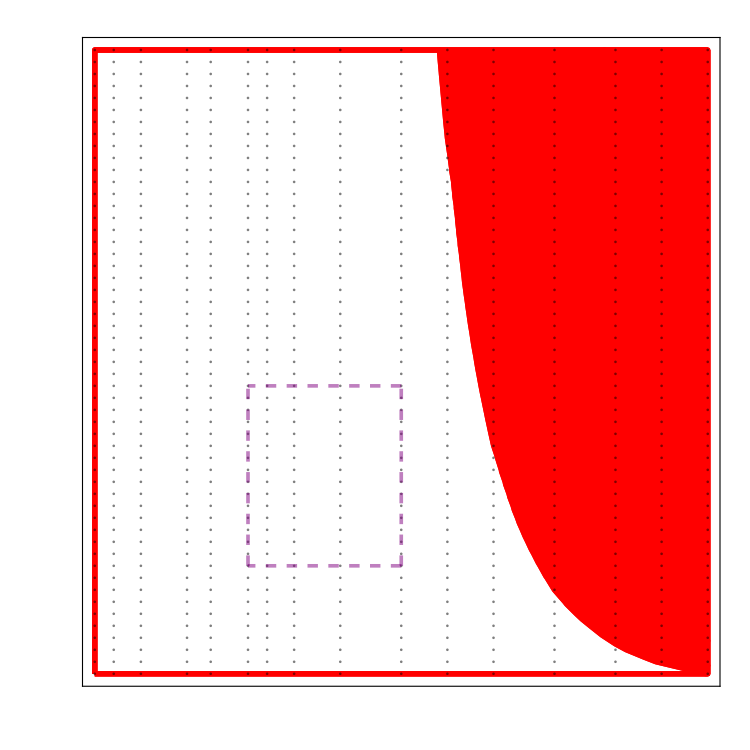

```mathematica
cfFull
```

## Explore Response Surfaces

```mathematica
i=5;
thresholdIx=i;
(**)
weeksRanges={{8,12},{12, 24},{24, 52},{52,1.5*52}};
(*colorsSolid=hexToRGB[#]&/@{"#0500c7","#0a4afc","#268cff","#75c1ff", "#c6ebff"};*)
(*colorsSolid={RGBColor[1, 0, 0],RGBColor[1, 0.56, 1],RGBColor[0, 0.8, 1],RGBColor[0.0006103608758678569, 0., 0.9347219043259327]};*)
colorsSolid={RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0]};
ColorBlendA[a_]:=Blend[{{1,Directive[colorsSolid[[1]],Opacity[0]]},{0,Directive[colorsSolid[[1]],Opacity[0]]}},a];
ColorBlendB[a_]:=Blend[{{1,Directive[colorsSolid[[2]],Opacity[0]]},{0,Directive[colorsSolid[[2]],Opacity[0]]}},a];
ColorBlendC[a_]:=Blend[{{1,Directive[colorsSolid[[3]],Opacity[0]]},{0,Directive[colorsSolid[[3]],Opacity[0]]}},a];
ColorBlendD[a_]:=Blend[{{1,Directive[colorsSolid[[4]],Opacity[0]]},{0,Directive[colorsSolid[[4]],Opacity[0]]}},a];
ColorBlendX[a_]:=Blend[{{1,Directive[colorsSolid[[4]],Opacity[0]]},{0,Directive[colorsSolid[[4]],Opacity[0]]}},a];
colors={ColorBlendA,ColorBlendB,ColorBlendC,ColorBlendD};
(**)
{thresholdIx,standingVar}={i,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuples={Log[N[#[[1,1]]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
(**)
yLabels=DeleteDuplicates[{Log[N[#[[1,2]]]],N[#[[1,2]]]}&/@filtered][[2;; ;;4]];
xLabels=DeleteDuplicates[{Log[N[#[[1,1]]]/1000000],NumberForm[N[#[[1,1]]]/1000000,{1,4}]}&/@filtered][[2;; ;;4]]
cf=Table[
ListDensityPlot[tuples
,BoundaryStyle->Directive[{Black, Thickness[.005]}]
,ClippingStyle->{RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0],RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0]}
,ColorFunction->(colors[[i]][#]&)
,ColorFunctionScaling->True
,Epilog->Flatten[{PointSize[Medium],Opacity[.2],(Point[#[[1;;2]]]&/@tuples)}]
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->None
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->750
,InterpolationOrder->2
,Mesh->False
,MeshStyle->Directive[White, Opacity[.25]]
,PlotLegends->None
,PlotRange->{All,All,weeksRanges[[i]]}(*{0, 260}}*)
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
]
,{i,1,Length[weeksRanges]}];
ca=ListContourPlot[tuples
,ClippingStyle->{White,White}
,Contours->50
,ContourStyle->Directive[{Black, Opacity[0]}]
,ColorFunction->(ColorBlend[#/weeksRanges[[-1,2]]]&)
,ColorFunctionScaling->False
,Epilog->Flatten[{
PointSize[.0025],Opacity[.5],(Point[#[[1;;2]]]&/@tuples),
Purple,Dashing[.01],Thickness[.0035],
Line[{{-4.605170185988091,10},{-4.605170185988091,25}}],
Line[{{-6.907755278982137,10},{-6.907755278982137,25}}],
Line[{{-4.605170185988091, 10},{-6.907755278982137,10}}],
Line[{{-4.605170185988091, 25},{-6.907755278982137,25}}]
}]
,FrameLabel->(Style[#,50]&/@{"Release Ratio","Weekly Releases"})
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
(*,FrameTicks->Automatic*)
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->1000
,InterpolationOrder->1
,Mesh->None
,MeshStyle->Directive[ White, Opacity[.25]]
(*,PlotLabel->Style["Weeks to: "<>ToString[thresholds[[thresholdIx]]],50,Black]*)
,PlotLegends->None
,PlotRange->{All,All,{Min[weeksRanges//Flatten],Max[weeksRanges//Flatten]}}(*{0, 260}}*)
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
];
cfFull=Show[ca,cf];
```

{{-8.92516,0.0001},{-6.90776,0.0010},{-4.60517,0.0100},{-1.38629,0.3000}}

```mathematica
(*Releases*)
expTuples=Tuples[{paramsRanges[[1]]/1000000*POPSIZE//N,paramsRanges[[2]]}];
relMosquitos={#[[1]],#[[2]],#[[1]]*#[[2]]}&/@expTuples;
tuplesB={Log[N[#[[1]]]/1000000],#[[2]],Log[N[#[[3]]]]}&/@relMosquitos;
(**)
yLabels=DeleteDuplicates[{Log[N[#[[1,2]]]],N[#[[1,2]]]}&/@filtered][[2;; ;;4]];
xLabels=DeleteDuplicates[{Log[N[#[[1,1]]]/1000000],NumberForm[N[#[[1,1]]]/1000000,{1,4}]}&/@filtered][[2;; ;;4]]
ca=ListContourPlot[tuplesB
,ClippingStyle->{White,White}
,Contours->50
,ContourStyle->Directive[{Black, Opacity[0]}]
,ColorFunction->(ColorBlend[#/17]&)
,ColorFunctionScaling->False
,Epilog->Flatten[{
PointSize[.0025],Opacity[.5],(Point[#[[1;;2]]]&/@tuples),
Purple,Dashing[.01],Thickness[.0035],
Line[{{-4.605170185988091,10},{-4.605170185988091,25}}],
Line[{{-6.907755278982137,10},{-6.907755278982137,25}}],
Line[{{-4.605170185988091, 10},{-6.907755278982137,10}}],
Line[{{-4.605170185988091, 25},{-6.907755278982137,25}}]
}]
,FrameLabel->(Style[#,50]&/@{"Release Ratio","Weekly Releases"})
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
(*,FrameTicks->Automatic*)
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->1000
,InterpolationOrder->1
,Mesh->None
,MeshStyle->Directive[ White, Opacity[.25]]
(*,PlotLabel->Style["Weeks to: "<>ToString[thresholds[[thresholdIx]]],50,Black]*)
,PlotLegends->None
,PlotRange->{All,All,All}(*{0, 260}}*)
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
];
cfFull=Show[ca,cf];
```

{{-8.92516,0.0001},{-6.90776,0.0010},{-4.60517,0.0100},{-1.38629,0.3000}}

{{-8.92516,0.0001},{-6.90776,0.0010},{-4.60517,0.0100},{-1.38629,0.3000}}

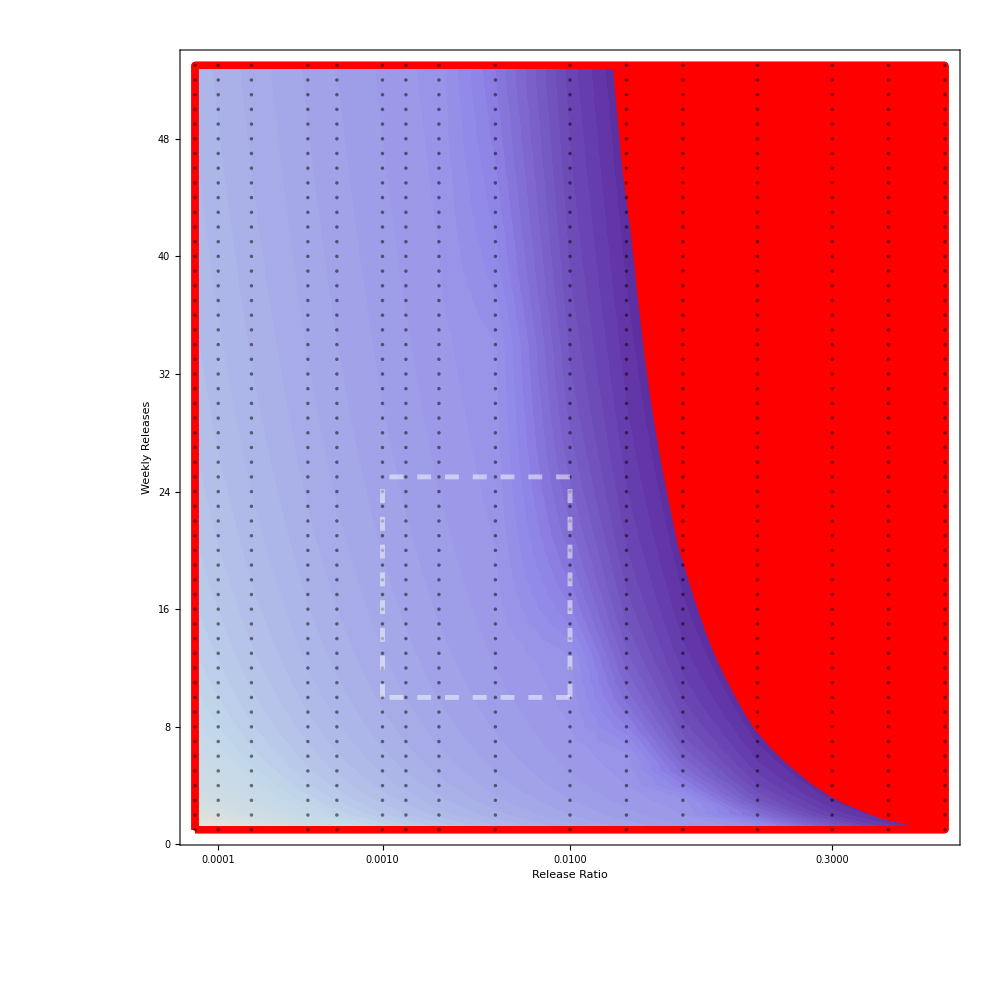

./img/CF_95.pdf

```mathematica
tuples={Log[N[#[[1,1]]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
(**)
yLabels=DeleteDuplicates[{Log[N[#[[1,2]]]],N[#[[1,2]]]}&/@filtered][[2;; ;;4]];
xLabels=DeleteDuplicates[{Log[N[#[[1,1]]]/1000000],NumberForm[N[#[[1,1]]]/1000000,{1,4}]}&/@filtered][[2;; ;;4]]
(**)
cost={#[[1,1]],#[[1,2]],#[[2,3]]/#[[1,3]]}&/@({tuplesB,tuples}//Transpose);
cPlot=ListContourPlot[cost
,ColorFunction->"LakeColors"
,ClippingStyle->{White,White}
,Contours->50
,ContourStyle->Directive[{Black, Opacity[0]}]
,ColorFunction->(ColorBlend[#]&)
,ColorFunctionScaling->True
,Epilog->Flatten[{
PointSize[.0025],Opacity[.5],(Point[#[[1;;2]]]&/@tuples),
White,Dashing[.01],Thickness[.0035],
Line[{{-4.605170185988091,10},{-4.605170185988091,25}}],
Line[{{-6.907755278982137,10},{-6.907755278982137,25}}],
Line[{{-4.605170185988091, 10},{-6.907755278982137,10}}],
Line[{{-4.605170185988091, 25},{-6.907755278982137,25}}]
}]
,FrameLabel->(Style[#,50]&/@{"Release Ratio","Weekly Releases"})
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
(*,FrameTicks->Automatic*)
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->1000
,InterpolationOrder->1
,Mesh->None
,MeshStyle->Directive[ White, Opacity[.25]]
(*,PlotLabel->Style["Weeks to: "<>ToString[thresholds[[thresholdIx]]],50,Black]*)
,PlotLegends->None
,PlotRangePadding->None
];
comb=Show[cPlot,cf]
Export["./img/CF_"<>StringPadRight[ToString[thresholds[[thresholdIx]]*100],2,"0"]<>".pdf",comb]
```

## Sweep Cost Responses

```mathematica
(**)
weeksRanges={{8,12},{12, 24},{24, 52},{52,1.5*52}};
(*colorsSolid=hexToRGB[#]&/@{"#0500c7","#0a4afc","#268cff","#75c1ff", "#c6ebff"};*)
(*colorsSolid={RGBColor[1, 0, 0],RGBColor[1, 0.56, 1],RGBColor[0, 0.8, 1],RGBColor[0.0006103608758678569, 0., 0.9347219043259327]};*)
colorsSolid={RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0]};
ColorBlendA[a_]:=Blend[{{1,Directive[colorsSolid[[1]],Opacity[0]]},{0,Directive[colorsSolid[[1]],Opacity[0]]}},a];
ColorBlendB[a_]:=Blend[{{1,Directive[colorsSolid[[2]],Opacity[0]]},{0,Directive[colorsSolid[[2]],Opacity[0]]}},a];
ColorBlendC[a_]:=Blend[{{1,Directive[colorsSolid[[3]],Opacity[0]]},{0,Directive[colorsSolid[[3]],Opacity[0]]}},a];
ColorBlendD[a_]:=Blend[{{1,Directive[colorsSolid[[4]],Opacity[0]]},{0,Directive[colorsSolid[[4]],Opacity[0]]}},a];
ColorBlendX[a_]:=Blend[{{1,Directive[colorsSolid[[4]],Opacity[0]]},{0,Directive[colorsSolid[[4]],Opacity[0]]}},a];
colors={ColorBlendA,ColorBlendB,ColorBlendC,ColorBlendD};
```

Thread::tdlen: Objects of unequal length in {{-8.92516,0.0001},{-6.90776,0.0010},{-4.60517,0.0100},{-1.38629,0.3000}} {{-9.21034,1,26.8952},{-9.21034,2,21.4354},{-9.21034,3,19.0099},{-9.21034,4,17.4534},{-9.21034,5,16.344},{-9.21034,6,15.5655},{-9.21034,7,14.9158},{-9.21034,8,14.3827},{-9.21034,9,13.9237},{-9.21034,10,13.5459},«31»,{-9.21034,42,10.0685},{-9.21034,43,10.0402},{-9.21034,44,9.99565},{-9.21034,45,9.95197},{-9.21034,46,9.92603},{-9.21034,47,9.91768},{-9.21034,48,9.87619},{-9.21034,49,9.83542},{-9.21034,50,9.82886},«798»} cannot be combined.

Thread::tdlen: Objects of unequal length in {{-8.92516,0.0001},{-6.90776,0.0010},{-4.60517,0.0100},{-1.38629,0.3000}} {{-9.21034,1,30.5557},{-9.21034,2,24.617},{-9.21034,3,21.9403},{-9.21034,4,20.2669},{-9.21034,5,19.0335},{-9.21034,6,18.1784},{-9.21034,7,17.4671},{-9.21034,8,16.8831},{-9.21034,9,16.3808},{-9.21034,10,15.9655},«31»,{-9.21034,42,12.0548},{-9.21034,43,12.038},{-9.21034,44,11.988},{-9.21034,45,11.939},{-9.21034,46,11.9079},{-9.21034,47,11.8776},{-9.21034,48,11.8312},{-9.21034,49,11.8025},{-9.21034,50,11.7745},«798»} cannot be combined.

Thread::tdlen: Objects of unequal length in {{-8.92516,0.0001},{-6.90776,0.0010},{-4.60517,0.0100},{-1.38629,0.3000}} {{-9.21034,1,35.0848},{-9.21034,2,28.5266},{-9.21034,3,25.572},{-9.21034,4,23.7004},{-9.21034,5,22.3437},{-9.21034,6,21.3942},{-9.21034,7,20.5855},{-9.21034,8,19.9606},{-9.21034,9,19.4049},{-9.21034,10,18.9435},«31»,{-9.21034,42,14.5035},{-9.21034,43,14.4627},{-9.21034,44,14.406},{-9.21034,45,14.3675},{-9.21034,46,14.3301},{-9.21034,47,14.2936},{-9.21034,48,14.2413},{-9.21034,49,14.1899},{-9.21034,50,14.173},«798»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

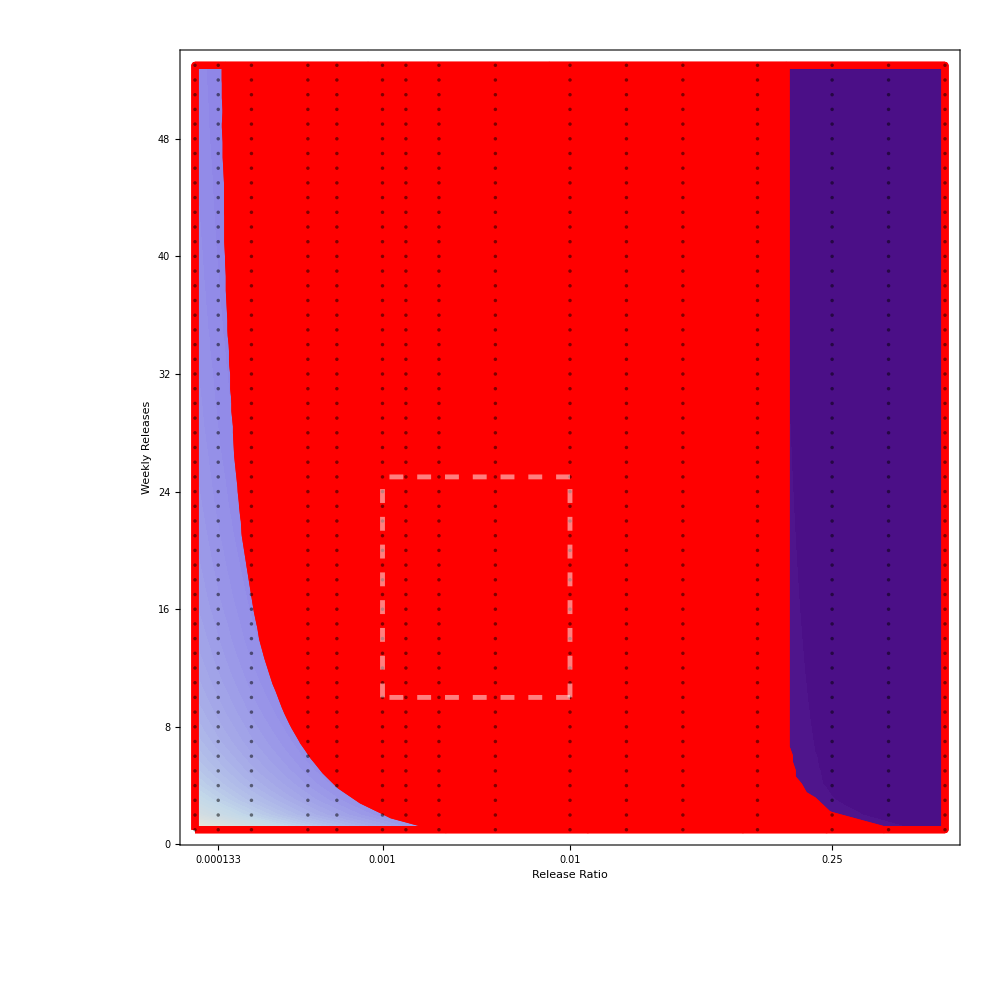
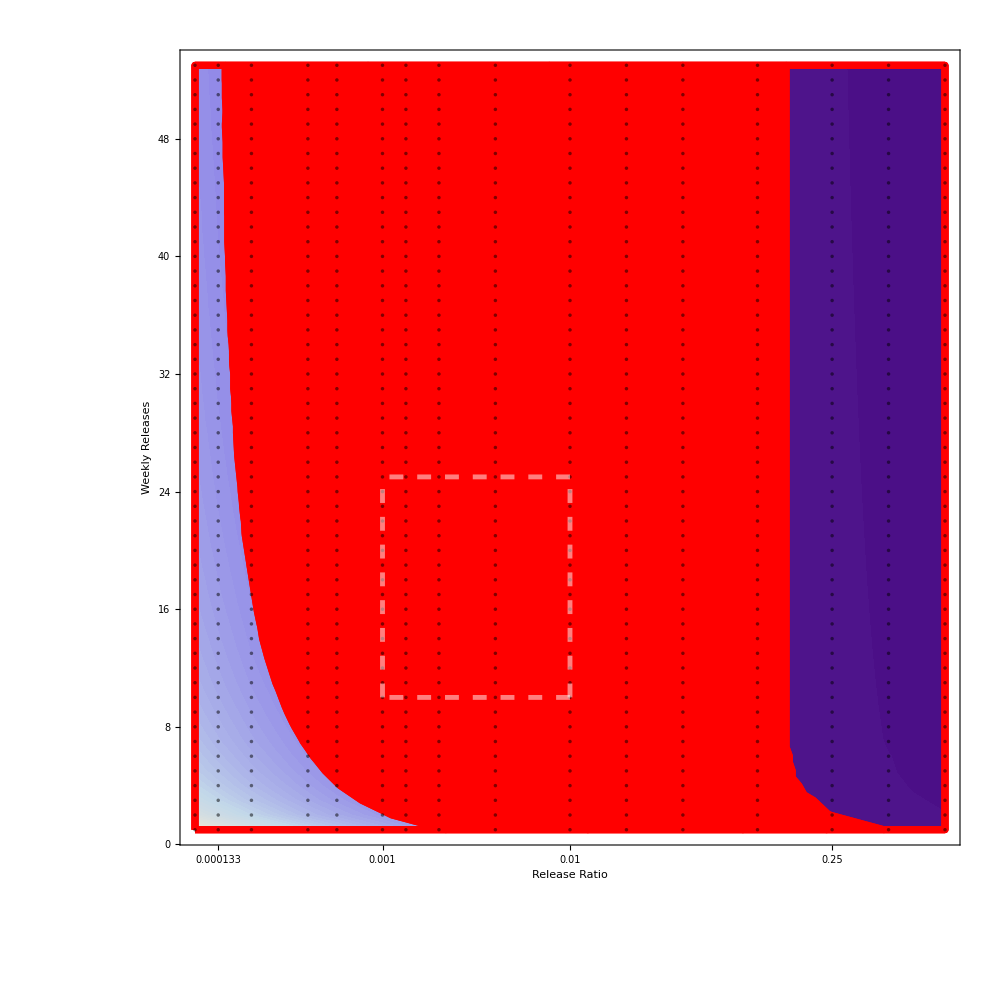
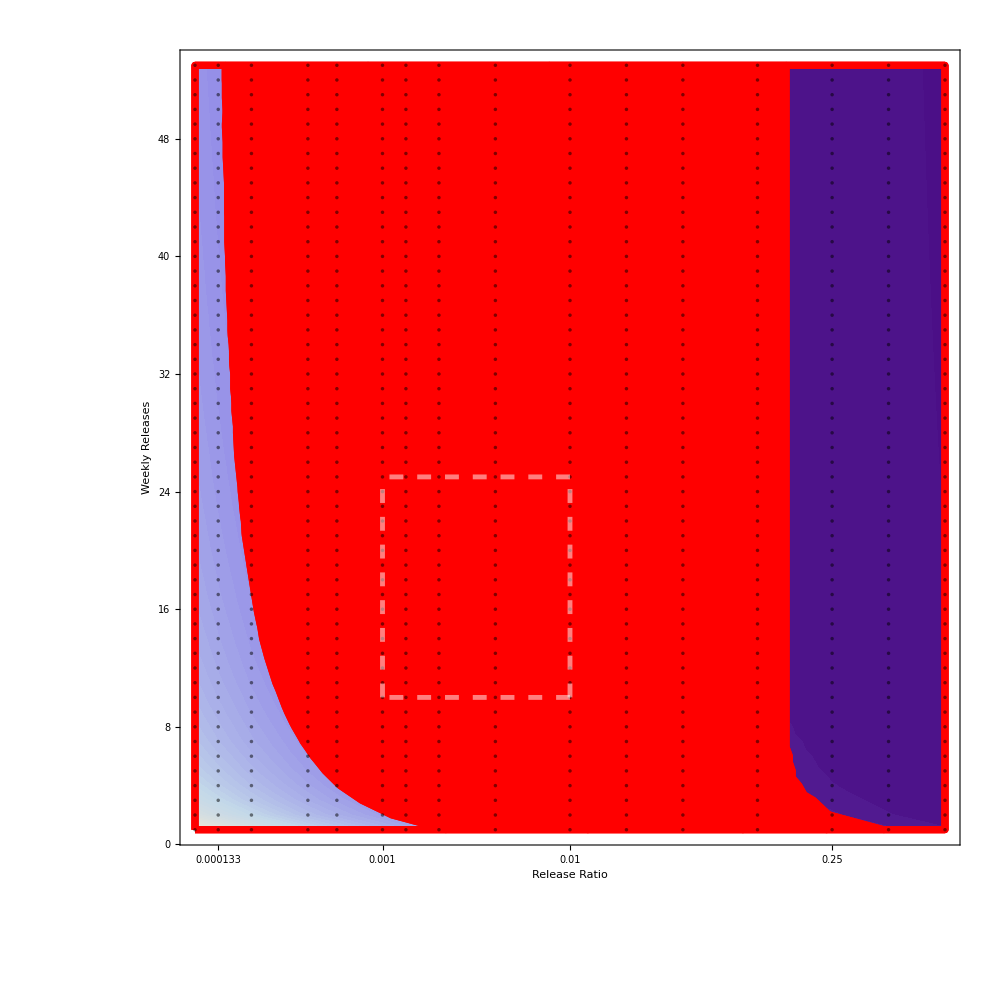
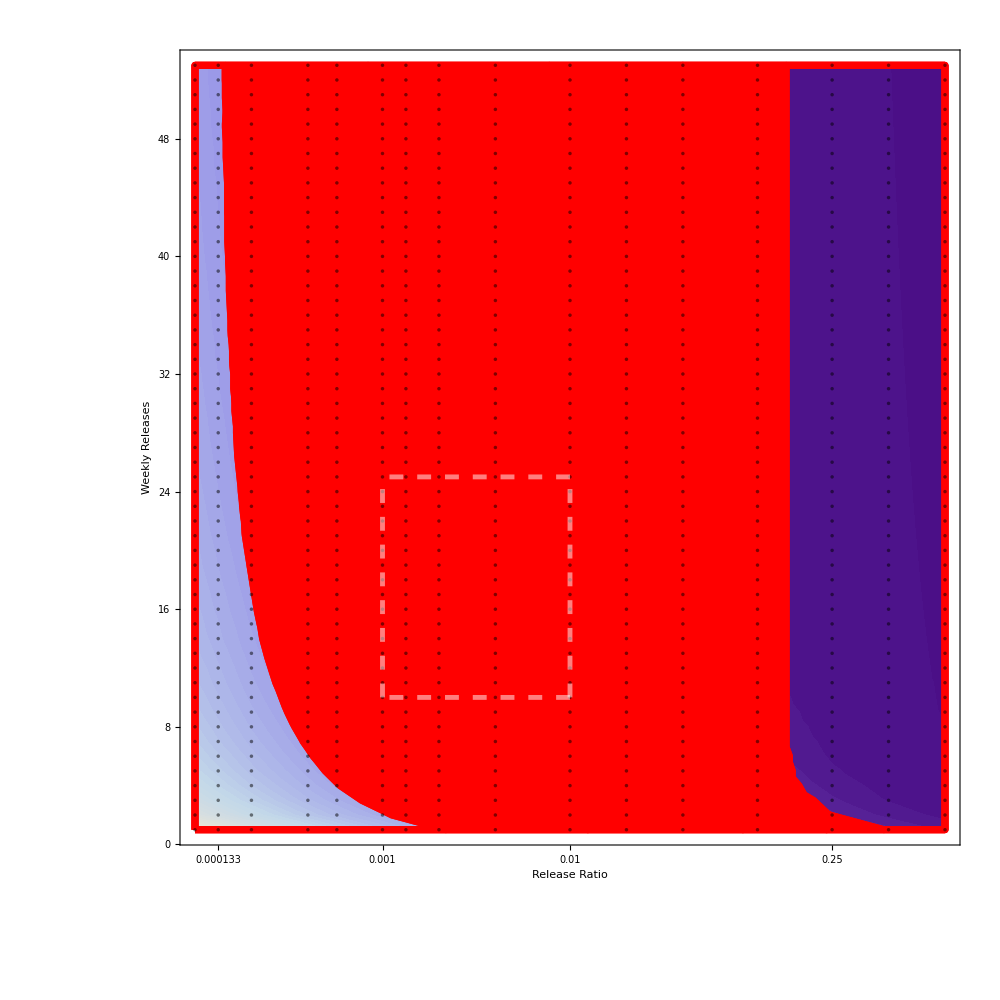
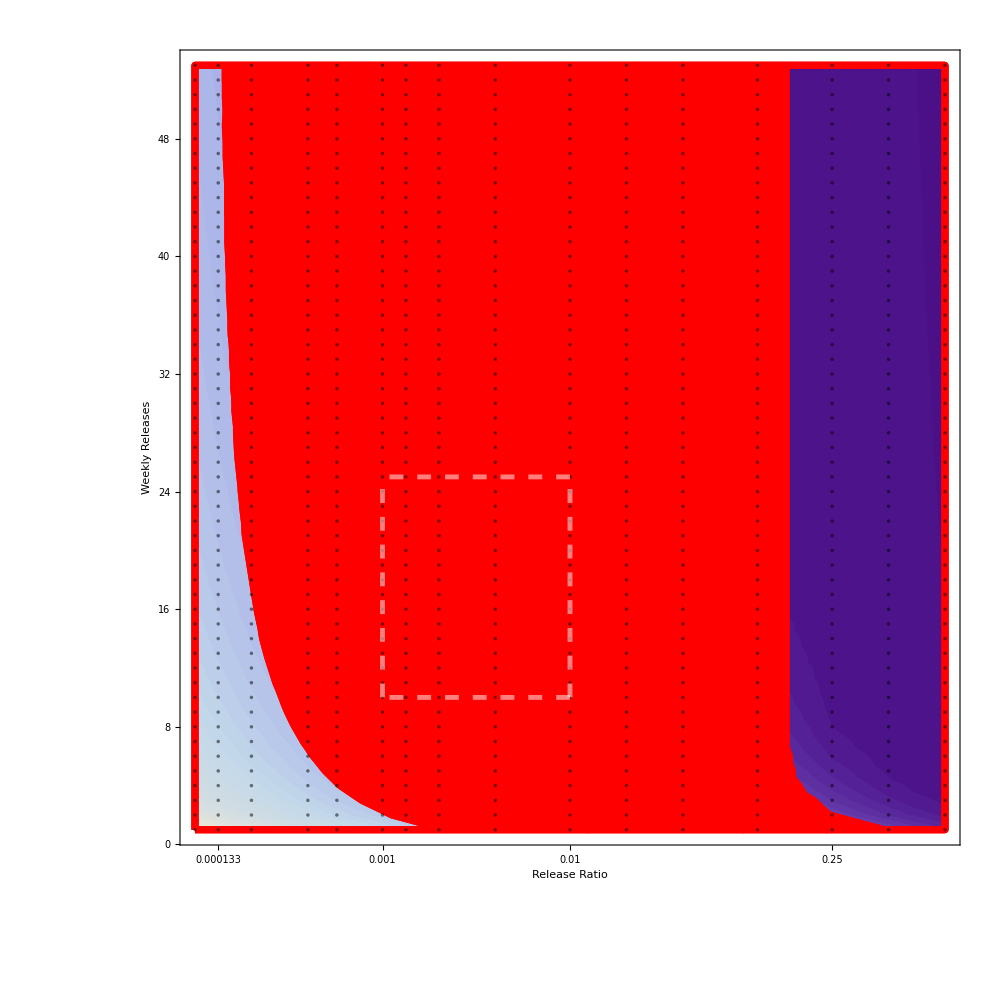

```mathematica
Table[
{thresholdIx,standingVar}={i,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];

,{i,1,5}]
(*Export["./img/CF_"<>StringPadRight[ToString[thresholds[[thresholdIx]]*100],2,"0"]<>".pdf",cPlot]*)
```

## Export Legend

```mathematica
range=Length[Range[Last[weeksRanges][[2]]-First[weeksRanges[[1]]]]-1];
labels=Range[weeksRanges[[1]],Last[weeksRanges][[2]],2];
blends=ColorBlend[#]&/@Range[0,1,1/range];
colorScale=Transpose[{
Reverse[ImageResize[Rasterize[#]//ImageCrop,50]&/@blends],
Reverse[Style[ToString[#],30]&/@Range[Min[weeksRanges//Flatten],Max[weeksRanges//Flatten]]]
}][[;;;;2]]//Grid;
Export["./img/legend.pdf",colorScale]
(**)
bar=BarLegend[{ColorBlend[#]&,{0,1}}
,LabelStyle->{FontSize->.001}
];
Export["./img/barLegend.pdf",bar]
```

./img/legend.pdf

./img/barLegend.pdf

## Interpolations

```mathematica
i=3;
{thresholdIx,standingVar}={i,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuples={N[#[[1,1]]]/1000000,#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
```

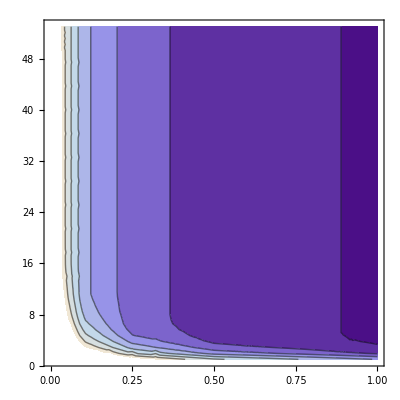

```mathematica
inputTriplets={{#[[1]],#[[2]]},#[[3]]}&/@tuples;
fInter=Interpolation[inputTriplets,Method->"Spline", InterpolationOrder->1];
ContourPlot[
fInter[x,y]
,{x,10^-4,1},{y,1,53}
,ColorFunction->"LakeColors"
]
```

```mathematica
ListPlot3D[tuples
,ColorFunction->"LakeColors"
,ImageSize->1500
,InterpolationOrder->0
,PlotRange->{{0,.1},{0,53},{0,80}}
]
```

-Graphics3D-

0.0631022

{0.0650556,12.5556}

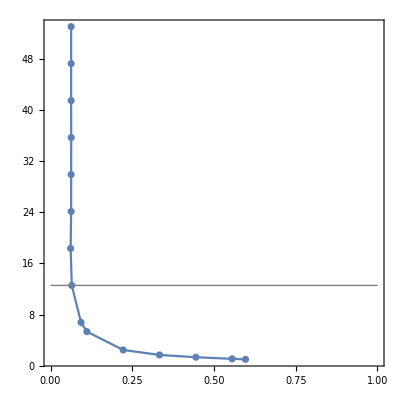

```mathematica
inputTriplets={{#[[1]],#[[2]]},#[[3]]}&/@tuples;
fInter=Interpolation[inputTriplets,Method->"Spline", InterpolationOrder->2];
region=ImplicitRegion[fInter[x,y]==15,{x,y}];
rp=RegionPlot[region,PlotRange->{{10^-4,1},{1,53}}];
pts=rp[[1,1,1]]//Sort;
quant=Quantile[pts[[All,1]],.25]
break=Sort[Cases[pts,{a_,b_}/;a<quant*1.05],#1[[2]]>#2[[2]]&][[-1]]
Show[{rp,pts//ListPlot}
,Epilog->{Gray,Line[{{0,break[[2]]},{1,break[[2]]}}]}
]
```

{{8,5.35962},{9,6.77778},{10,12.5556},{11,12.5556},{12,10.5023},{13,12.5556},{14,12.5556},{15,12.5556},{16,12.5556},{17,18.3333},{18,18.3333},{19,18.3333},{20,18.3333}}

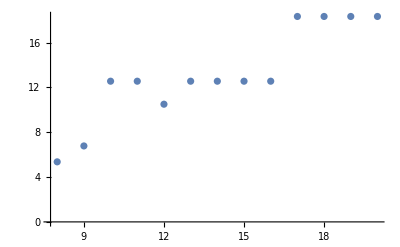

```mathematica
sweep=Table[
region=ImplicitRegion[fInter[x,y]==i,{x,y}];
rp=RegionPlot[region,PlotRange->{{10^-4,1},{1,53}}];
pts=rp[[1,1,1]]//Sort;
quant=Quantile[pts[[All,1]],.25];
break=Sort[Cases[pts,{a_,b_}/;a<quant*1.05],#1[[2]]>#2[[2]]&][[-1]];
{i,break[[2]]}
,{i,8,20}]
ListPlot[sweep]
```

## Compare Responses

```mathematica
i=1;
(**)
{thresholdIx,standingVar}={i,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuples={Log[N[#[[1,1]]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
```

```mathematica
{dataA,dataB}={
ReadDataset["/Volumes/marshallShare/UCI/Yoosook/yParams/island/thresholdCrosses.csv"],
ReadDataset["/Volumes/marshallShare/UCI/Yoosook/yParams/islandMixed/thresholdCrosses.csv"]
};
```

```mathematica
transposedDatasets=({dataA,dataB}//Transpose);
diff={#[[1,1]],#[[2,2]]-#[[1,2]]}&/@transposedDatasets;
```